#### Лабораторная работа 4 Интерполяция и среднеквадратичное приближение Вариант 8

Задание 1.  Создать таблицу значений функции f(x) , разбив отрезок [0, 6] на n равных частей точками x_i ( i = OverBar[0, n]).  Для полученной таблично заданной в 
равноотстоящих узлах функции f (x), выполнить следующие действия при n = 6 и n = 10: 
	а) построить интерполяционный многочлен Лагранжа L_n(x), проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и L_n(x) на одном чертеже); 
	б) создать таблицу конечных разностей функции f(x) по точкам (x_i, f(x_i)), i = OverBar[0,n]; 
	в)  построить второй интерполяционный многочлен Ньютона P_n(x),  проиллюстрировать графически; 
	г)  построить интерполяционный многочлен Ньютона Np_n(x) с помощью 
функции InterpolatingPolynomial пакета Mathematica, проиллюстрировать графически; 
	д) вычислить значения функции f(x) и всех построенных интерполяционных многочленов L_n(x), P_n(x) и Np_n(x) в точке x = 2,4316;
	е) построить график погрешности интерполирования многочленом Ньютона 
R_n(x)=|f(x)-Np_n(x)| на отрезке [0, 6], найти максимум погрешности R_n(x) на отрезке [0, 6] с помощью  функции FindMaximum пакета Mathematica; 
	ж)  исследовать зависимость погрешности интерполирования R_n(x) от 
числа узлов интерполяции (степени многочлена n).

	1.8. f(x) = exp(2x-(2 x^2)/7)*arctg((3 x^5)/14+5/6).

```mathematica
f[x_]= Exp[2x-(2x^2)/7]*ArcTan[(3x^5)/14+5/6];
```

```mathematica
a = 0; b = 6; n1 = 6; n2=10; h1 = (b-a)/n1; h2 = (b-a)/n2;
```

```mathematica
data1 = N[Table[{a+i*h1, f[a+i*h1]},{i, 0, n1}]]
```

{{0.,0.694738},{1.,4.4902},{2.,25.0988},{3.,47.849},{4.,48.2917},{5.,27.3243},{6.,8.71884}}

```mathematica
data = N[Table[{a+i*h2, f[a+i*h2]},{i, 0, n2}]]
```

{{0.,0.694738},{0.6,2.11037},{1.2,6.85994},{1.8,19.8499},{2.4,35.5054},{3.,47.849},{3.6,51.616},{4.2,45.1195},{4.8,32.0584},{5.4,18.5322},{6.,8.71884}}

а) Введём вспомогательные обозначения P(x):

```mathematica
P1[x_]=∏_(i=0)^n1 (x-data1[[i+1,1]])
```

(-6.+x) (-5.+x) (-4.+x) (-3.+x) (-2.+x) (-1.+x) (0.+x)

```mathematica
P2[x_]=∏_(i=0)^n2 (x-data[[i+1,1]])
```

(-6.+x) (-5.4+x) (-4.8+x) (-4.2+x) (-3.6+x) (-3.+x) (-2.4+x) (-1.8+x) (-1.2+x) (-0.6+x) (0.+x)

Используя заданные обозначения, зададим формулы интерполяционного многочлена Лагранжа:

```mathematica
L1[x_]= Sum[data1[[i+1,2]] P1[x]/((x-data1[[i+1,1]]) P1'[data1[[i+1,1]]]),{i,0,n1}]//Simplify
```

0.694738+6.23309 x-17.6804 x^2+21.9917 x^3-7.77259 x^4+1.07592 x^5-0.0522147 x^6

```mathematica
L2[x_]= Sum[data[[i+1,2]] P2[x]/((x-data[[i+1,1]]) P2'[data[[i+1,1]]]),{i,0,n2}]//Simplify
```

0.694738+20.9618 x-73.3036 x^2+104.474 x^3-72.426 x^4+30.971 x^5-8.57071 x^6+1.50135 x^7-0.157772 x^8+0.00891435 x^9-0.00020273 x^10

Проиллюстрируем полученные интерполяционные многочлены.
	n = 6:

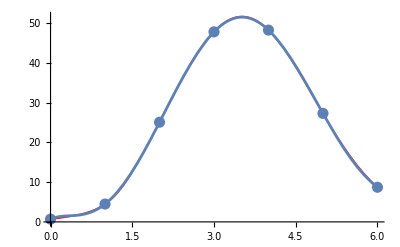

```mathematica
graph=Plot[f[x],{x,a,b},PlotStyle->{Red,Thick}];
graphD1=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}];
graphL1=Plot[L1[x],{x,a,b}];
Show[graph,graphD1,graphL1]
```

n = 10:

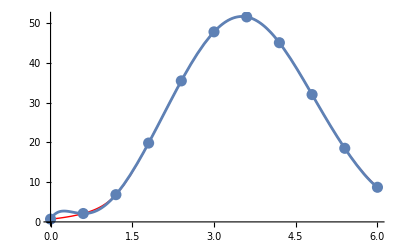

```mathematica
graphD2=ListPlot[data,PlotStyle->{Darker,PointSize[0.02]}];
graphL2=Plot[L2[x],{x,a,b}];
Show[graph,graphD2,graphL2]
```

б) Создадим массивы dif размера (n+1)*(n+1), в котором будем хранить конечные разности.

```mathematica
tab1=Array[dif1,{n1+1,n1+1}, {0,0}];
For[k=1,k<=n1,k++,For[i=n1,i>=n1-k,i--,dif1[i,k]=""]];
For[i=0, i<=n1,i++,dif1[i,0]=data1[[i+1,2]]];
For[k=1,k<=n1,k++,For[i=0,i<=n1-k,i++,dif1[i,k]=dif1[i+1,k-1]-dif1[i,k-1]]];
```

```mathematica
tab2=Array[dif2,{n2+1,n2+1}, {0,0}];
For[k=1,k<=n2,k++,For[i=n2,i>=n2-k,i--,dif2[i,k]=""]];
For[i=0, i<=n2,i++,dif2[i,0]=data[[i+1,2]]];
For[k=1,k<=n2,k++,For[i=0,i<=n2-k,i++,dif2[i,k]=dif2[i+1,k-1]-dif2[i,k-1]]];
```

Выведем полученные таблицы конечных разностей:

n = 6:

```mathematica
PaddedForm[TableForm[tab1],{n1,n1-1}]
```

9.69196 | -17.18080 |  3.32077 |  3.90549 |  0.77509 | -0.03721 | -0.05940
 19.64460 | -22.57080 | -8.10195 |  0.62964 |  0.97120 |  0.31025 | 
 43.20500 | -3.56774 | -10.39830 | -3.92626 | -0.66392 |  | 
 47.84900 |  23.50230 |  3.92131 | -1.12024 |  |  | 
 17.25710 |  14.30490 |  7.19778 |  |  |  | 
 2.32508 |  2.62195 |  |  |  |  | 
 0.80622 |  |  |  |  |  |

n = 10:

```mathematica
PaddedForm[TableForm[tab2],{n2,n2-1}]
```

9.105080883 | -14.422201170 |  6.364965918 |  1.849490228 | -1.037877825 | -0.367142116 |  0.003071001 |  0.023815701 |  0.007643726 |  0.002471607 |  0.001206752
 12.574605870 | -18.891779550 |  3.872700392 |  4.054219484 |  0.052337592 | -0.378856946 | -0.106276093 | -0.016212298 | -0.006440384 | -0.004695208 | 
 21.295944200 | -23.178756390 | -3.764226020 |  3.911395640 |  1.406407801 |  0.083531040 | -0.025277106 |  0.018937975 |  0.020314603 |  | 
 36.253804620 | -17.825834810 | -12.632332790 | -0.465973247 |  1.081541289 |  0.198150014 | -0.119893972 | -0.087443769 |  |  | 
 50.099572270 |  2.662829365 | -11.482720820 | -3.974325445 |  0.310901968 |  0.719786919 |  0.281594194 |  |  |  | 
 47.848955100 |  22.073167140 | -1.677582537 | -4.941991153 | -2.261683893 | -0.354399751 |  |  |  |  | 
 29.192765650 |  24.794075920 |  9.527140593 |  1.229908945 | -1.209306474 |  |  |  |  |  | 
 9.934592440 |  11.245995610 |  7.210363186 |  3.798798364 |  |  |  |  |  |  | 
 2.677256031 |  3.264314397 |  2.091323322 |  |  |  |  |  |  |  | 
 1.170294224 |  1.795754531 |  |  |  |  |  |  |  |  | 
 0.738292538 |  |  |  |  |  |  |  |  |  |

в) Построим вторые интерполяционные многочлены Ньютона P_n(x):

n = 6:

```mathematica
q1=(x-b)/h1;pn1[x_]=dif1[n1,0];p1[q_]=1;
For[k=1,k≤n1,k++,p1[q_]=p1[q1]*(q1+k-1);pn1[x_]=pn1[x]+dif1[n1-k,k]/(k!) p1[q1]];
pn1[x]//Simplify
```

0.694738+6.23309 x-17.6804 x^2+21.9917 x^3-7.77259 x^4+1.07592 x^5-0.0522147 x^6

n = 10:

```mathematica
q2=(x-b)/h2;pn2[x_]=dif2[n2,0];p2[q_]=1;
For[k=1,k≤n2,k++,p2[q_]=p2[q2]*(q2+k-1);pn2[x_]=pn2[x]+dif2[n2-k,k]/(k!) p2[q2]];
pn2[x]//Simplify
```

0.694738+20.9618 x-73.3036 x^2+104.474 x^3-72.426 x^4+30.971 x^5-8.57071 x^6+1.50135 x^7-0.157772 x^8+0.00891435 x^9-0.00020273 x^10

Проиллюстрируем полученные многочлены:

n = 6:

```mathematica
graphPn1=Plot[pn1[x],{x,a,b}];
Show[graph,graphD1,graphPn1]
```

-Graphics-

n = 10:

```mathematica
graphPn2=Plot[pn2[x],{x,a,b}];
Show[graph,graphD2,graphPn2]
```

-Graphics-

г) Построим интерполяционные многочлены Ньютона Np_n(x)  с помощью функции InterpolatingPolynomial:

```mathematica
Np1[x_]=InterpolatingPolynomial[data1,x]//Simplify
```

0.694738+6.23309 x-17.6804 x^2+21.9917 x^3-7.77259 x^4+1.07592 x^5-0.0522147 x^6

```mathematica
Np2[x_]=InterpolatingPolynomial[data,x]//Simplify
```

0.694738+20.9618 x-73.3036 x^2+104.474 x^3-72.426 x^4+30.971 x^5-8.57071 x^6+1.50135 x^7-0.157772 x^8+0.00891435 x^9-0.00020273 x^10

Проиллюстрируем полученные многочлены:

n = 6:

```mathematica
graphNp1=Plot[Np1[x],{x,a,b}];
Show[graph,graphD1,graphNp1]
```

-Graphics-

n = 10:

```mathematica
graphNp2=Plot[Np2[x],{x,a,b}];
Show[graph,graphD2,graphNp2]
```

-Graphics-

д) Вычислим значения функции f(x) и всех построенных интерполяционных многочленов L_n(x), P_n(x)  и Np_n(x) в точке x=2,4316:

```mathematica
f[2.4316]
```

36.288

n = 6:

```mathematica
L1[2.4316]
```

36.4334

```mathematica
pn1[2.4316]
```

36.4334

```mathematica
Np1[2.4316]
```

36.4334

n = 10:

```mathematica
L2[2.4316]
```

36.2906

```mathematica
pn2[2.4316]
```

36.2906

```mathematica
Np2[2.4316]
```

36.2906

е) Найдём погрешность интерполирования многочленом Ньютона на отрезке [0,6]:

n=6:

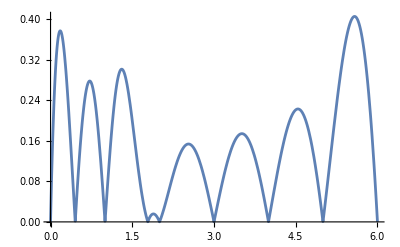

```mathematica
Rn1[x_]=Abs[f[x]-Np1[x]];
graphRn1=Plot[Rn1[x],{x,a,b}]
```

```mathematica
maxRn1=FindMaximum[Rn1[x],{x,a,b}]
```

{0.377551,{x→0.177576}}

n=10:

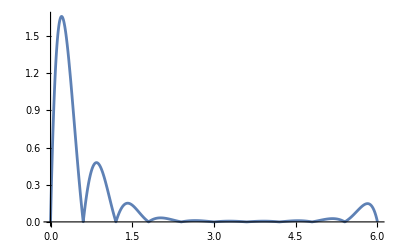

```mathematica
Rn2[x_]=Abs[f[x]-Np2[x]];
graphRn2=Plot[Rn2[x],{x,a,b}, PlotRange->Full]
```

```mathematica
maxRn2=FindMaximum[Rn2[x],{x,a,b}]
```

{1.65976,{x→0.202919}}

ж) Погрешность интерполяции уменьшается с увеличением числа узлов.

Задание 2. Создать таблицу значений функции f(x), разбив отрезок [0; 6] на n частей неравноотстоящими точками x_i вида (a + b)/2+(b - a)/2*t_i, где t_i – корни многочлена Чебышёва T_(n+1)(t) (i = OverBar[0,n]). Для полученной таблично заданной функции f(x), выполнить следующие действия при n = 6 и n = 10:
	а) создать таблицу разделенных разностей функции f(x) по точкам (x_i, f(x_i)), i = OverBar[0,n];
	б) построить интерполяционный многочлен Ньютона Pnr_n(x) для неравноотстоящих узлов, проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Pnr_n(x) на одном чертеже);
	в) построить интерполирующую функцию Intf_n(x) с помощью функции Interpolation пакета Mathematica, проиллюстрировать графически;
	г) вычислить значения функции f(x) и построенных интерполяционных многочленов Pnr[n](x) и Intf_n(x) в точке x = 2,4316;
	д) найти максимумы абсолютных погрешностей интерполирования функции f(x) многочленом Ньютона Pnr_n(x) и функцией Intf_n(x) на отрезке [0; 6] с помощью функции FindMaximum пакета Mathematica.

Многочлен Чебышёва для n1 и n2:

```mathematica
Ch1[y_]=Cos[(Pi (2* y+1))/(2*n1+2)];
```

```mathematica
Ch2[y_]=Cos[(Pi (2 *y+1))/(2*n2+2)];
```

```mathematica
data1=Table[{x1=(a+b)/2+(b-a)/2*Ch1[y],f[x1]},{y,0,n1}]//N
```

{{5.92478,9.69196},{5.34549,19.6446},{4.30165,43.205},{3.,47.849},{1.69835,17.2571},{0.654506,2.32508},{0.0752163,0.806216}}

```mathematica
data2=Table[{x2=(a+b)/2+(b-a)/2*Ch2[i],f[x2]},{i,0,n2}]//N
```

{{5.96946,9.10508},{5.7289,12.5746},{5.26725,21.2959},{4.62192,36.2538},{3.8452,50.0996},{3.,47.849},{2.1548,29.1928},{1.37808,9.93459},{0.732751,2.67726},{0.271104,1.17029},{0.0305357,0.738293}}

а) Создадим массивы dif размера (n+1)*(n+1), в котором будем хранить разделённые разности.

```mathematica
tab1=Array[dif1,{n1+1,n1+1}, {0,0}];
For[k=1,k<=n1,k++,For[i=n1,i>=n1-k,i--,dif1[i,k]=""]];
For[i=0, i<=n1,i++,dif1[i,0]=data1[[i+1,2]]];
For[k=1,k<=n1,k++,For[i=0,i<=n1-k,i++,dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(data1[[i+1+k,1]]-data1[[i+1,1]])]];
```

```mathematica
tab2=Array[dif2,{n2+1,n2+1}, {0,0}];
For[k=1,k<=n2,k++,For[i=n2,i>=n2-k,i--,dif2[i,k]=""]];
For[i=0, i<=n2,i++,dif2[i,0]=data2[[i+1,2]]];
For[k=1,k<=n2,k++,For[i=0,i<=n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(data2[[i+1+k,1]]-data2[[i+1,1]])]];
```

Выведем полученные таблицы разделённых разностей:

n = 6:

```mathematica
PaddedForm[TableForm[tab1],{n1,n1-1}]
```

0.69474 |  3.79546 |  16.81320 | -14.67170 | -9.77726 |  35.12340 | -37.59460
 4.49020 |  20.60860 |  2.14151 | -24.44890 |  25.34610 | -2.47121 | 
 25.09880 |  22.75010 | -22.30740 |  0.89723 |  22.87490 |  | 
 47.84900 |  0.44274 | -21.41020 |  23.77220 |  |  | 
 48.29170 | -20.96740 |  2.36199 |  |  |  | 
 27.32430 | -18.60540 |  |  |  |  | 
 8.71884 |  |  |  |  |  |

n = 10:

```mathematica
PaddedForm[TableForm[tab2],{n2,n2-1}]
```

0.694738276 |  1.415633955 |  3.333935304 |  4.906488380 | -10.481414720 |  10.078883830 | -8.963416795 |  10.712423380 | -13.517081000 |  12.582409510 | -4.448291110
 2.110372231 |  4.749569259 |  8.240423684 | -5.574926345 | -0.402530897 |  1.115467033 |  1.749006586 | -2.804657618 | -0.934671494 |  8.134118396 | 
 6.859941490 |  12.989992940 |  2.665497339 | -5.977457241 |  0.712936137 |  2.864473620 | -1.055651031 | -3.739329111 |  7.199446902 |  | 
 19.849934430 |  15.655490280 | -3.311959902 | -5.264521105 |  3.577409756 |  1.808822588 | -4.794980142 |  3.460117791 |  |  | 
 35.505424720 |  12.343530380 | -8.576481007 | -1.687111349 |  5.386232344 | -2.986157554 | -1.334862352 |  |  |  | 
 47.848955100 |  3.767049374 | -10.263592360 |  3.699120996 |  2.400074790 | -4.321019906 |  |  |  |  | 
 51.616004470 | -6.496542981 | -6.564471360 |  6.099195786 | -1.920945116 |  |  |  |  |  | 
 45.119461490 | -13.061014340 | -0.465275574 |  4.178250670 |  |  |  |  |  |  | 
 32.058447150 | -13.526289920 |  3.712975096 |  |  |  |  |  |  |  | 
 18.532157230 | -9.813314819 |  |  |  |  |  |  |  |  | 
 8.718842414 |  |  |  |  |  |  |  |  |  |

б) Введём вспомогательные обозначения P(x):

```mathematica
P1[x_]=1;P2[x_]=1;Pnr1[x_]=dif1[0,0];Pnr2[x_]=dif2[0,0];
```

```mathematica
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-data1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+dif1[0,i+1] P1[x]]
```

```mathematica
Pnr1[x]//Simplify
```

0.213126+9.43457 x-22.4277 x^2+24.9489 x^3-8.66824 x^4+1.20573 x^5-0.0594004 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x] (x-data2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+dif2[0,i+1] P2[x]]
```

```mathematica
Pnr2[x]//Simplify
```

0.785621-2.27209 x+25.4244 x^2-60.3115 x^3+72.8853 x^4-45.108 x^5+16.3085 x^6-3.63502 x^7+0.493087 x^8-0.0373144 x^9+0.00120675 x^10

Проиллюстрируем полученные многочлены:

n = 6:

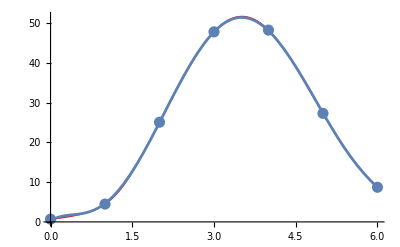

```mathematica
graphPnr1=Plot[Pnr1[x],{x,a,b}];
Show[graph,graphD1,graphPnr1]
```

n = 10:

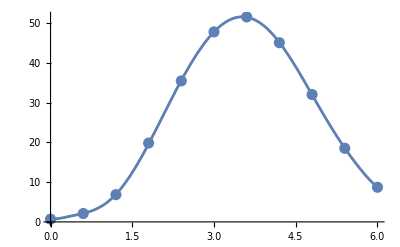

```mathematica
graphPnr2=Plot[Pnr2[x],{x,a,b}];
Show[graph,graphD2,graphPnr2]
```

в) Построим интерполирующие функции с помощью встроенной функции Interpolation:

```mathematica
Intf1=Interpolation[data1];
Intf2=Interpolation[data2];
```

Проиллюстрируем полученные интерполирующие функции:

n = 6:

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

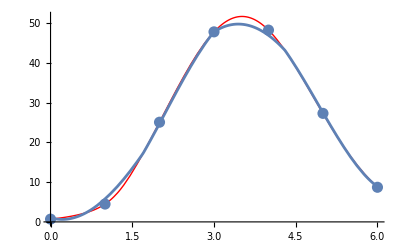

```mathematica
graphIntf1=Plot[Intf1[x],{x,a,b}];
Show[graph,graphD1,graphIntf1]
```

n = 10:

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

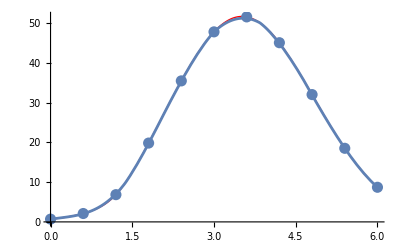

```mathematica
graphIntf2=Plot[Intf2[x],{x,a,b}];
Show[graph,graphD2,graphIntf2]
```

г) Вычислим значения функции f(x) и всех построенных интерполяционных многочленов Pnr_n(x)  и Intf_n(x) в точке x=2,4316:

```mathematica
f[2.4316]
```

36.288

n = 6:

```mathematica
Pnr1[2.4316]
```

36.4219

```mathematica
Intf1[2.4316]
```

35.7639

n = 10:

```mathematica
Pnr2[2.4316]
```

36.4431

```mathematica
Intf2[2.4316]
```

36.2253

д) Найдём погрешность интерполирования многочленом Ньютона и интерполирующей функцией на отрезке [0,6]:

n=6:

```mathematica
Rpn1[x_]=Abs[f[x]-Pnr1[x]];
```

```mathematica
maxRpn1=FindMaximum[Rpn1[x],{x,a,b}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMaximum[Rpn1[x],{x,a,b}]

```mathematica
Rintf1[x_]=Abs[f[x]-Intf1[x]];
```

```mathematica
maxRintf1=FindMaximum[Rintf1[x],{x,a,b}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.554166,{x→0.349672}}

n=10:

```mathematica
Rpn2[x_]=Abs[f[x]-Pnr2[x]];
```

```mathematica
maxRn2=FindMaximum[Rn2[x],{x,a,b}]
```

{1.65976,{x→0.202919}}

```mathematica
Rintf2[x_]=Abs[f[x]-Intf2[x]];
```

```mathematica
maxRintf2=FindMaximum[Rintf2[x],{x,a,b}]
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.0230782,{x→0.13683}}

Задание 3. Сравнить результаты заданий 1 и 2 для равноотстоящих и неравноотстоящих узлов и сделать выводы о зависимость погрешности интерполирования от числа узлов и их расположения на отрезке.

Число узлов: Увеличение числа узлов обычно приводит к уменьшению погрешности интерполяции, но важно учитывать распределение узлов.
Расположение узлов: Неравноотстоящие узлы, такие как узлы Чебышёва, могут значительно уменьшить погрешность интерполяции по сравнению с равноотстоящими узлами, особенно на краях интервала.

Задание 4. Используя таблицу значений функции f(x) в равноотстоящих точках отрезка [0, 6], полученной в задании 1 при 
n = 10, выполнить следующие действия:
	а) построить интерполяционный кубический сплайн дефекта 1 S_3(x) для функции f(x), проиллюстрировать графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и S_3(x) на одном чертеже);
	б) выполнить интерполяцию сплайном Sf(x) с помощью функции
Interpolation[data, Method->”Spline”], проиллюстрировать 	графически;
	в) построить интерполяционный кубический сплайн Spl с помощью функции SplineFit[data, Cubic] (предварительно загрузить пакет сплайн-интерполяции командой Needs[“Splines`”]), проиллюстрировать графически (для построения графика сплайна Spl использовать функцию ParametricPlot);
	г) вычислить значения функции f(x) и построенных интерполяционных сплайнов S_3(x), Sf(x) иSpl в точке x = 2,4316.

а) Для получения кубического сплайна дефекта 1 найдём коэффициенты c_k с помощью встроенной функции LinearSolve.

```mathematica
list=Table[0,{i,0,n2}];
```

```mathematica
A=Table[0,{n2-1},{n2-1}];
```

```mathematica
Do[If[i≠1,A[[i,i-1]]=h2];A[[i,i]]=4 h2;If[i≠n2-1,A[[i,i+1]]=h2],{i,1,n2-1}]
```

```mathematica
A//MatrixForm//N
```

(2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4 | 0.6
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.6 | 2.4)

```mathematica
B=Table[3 ((data[[i,2]]-data[[i-1,2]])/h2-(data[[i-1,2]]-data[[i-2,2]])/h2),{i,3,n2+1}]//N;
```

```mathematica
B//MatrixForm//N
```

(16.6697
41.2021
13.3275
-16.5598
-42.8824
-51.318
-32.8224
-2.32638
18.5649)

```mathematica
X=LinearSolve[A,B];
```

```mathematica
For[i=1,i≤n2-1,i++,list[[i+1]]=X[[i]]];
```

```mathematica
MatrixForm[list]
```

(0
3.01149
15.7368
2.71139
-4.36991
-12.8314
-15.7752
-9.59787
-0.537277
7.86968
0)

Зададим также коэффициенты a_k, b_k и d_k кубического сплайна:

```mathematica
listA=Table[data[[i,2]],{i,1,n2}]
```

{0.694738,2.11037,6.85994,19.8499,35.5054,47.849,51.616,45.1195,32.0584,18.5322}

```mathematica
listB=Table[(data[[i,2]]-data[[i-1,2]])/h2+2/3 h2 list[[i]]+1/3 h2 list[[i-1]],{i,2,n2+1}]
```

{3.56399,14.813,25.8819,24.8868,14.566,-2.59793,-17.8218,-23.9028,-19.5034,-14.7816}

```mathematica
listD=Table[(list[[i]]-list[[i-1]])/(3 h2),{i,2,n2+1}]
```

{1.67305,7.06963,-7.23635,-3.93406,-4.70082,-1.63543,3.43183,5.03366,4.67053,-4.37205}

Теперь зададим кубический сплайн в виде кусочно заданной функции:

```mathematica
splineData=Table[{listA[[i]]+listB[[i]] (x-data[[i+1,1]])+listC[[i+1]] (x-data[[i+1,1]])^2+listD[[i]] (x-data[[i+1,1]])^3,data[[i,1]]≤x≤data[[i+1,1]]}, {i,1,n2}]//Simplify;
S[x_]=Piecewise[splineData]
```

Piecewise[{{-1.73605+5.14096 x-2.81989 x^2+1.67305 x^3, 0.≤x≤0.6}, {-27.6988+45.0492 x-25.3238 x^2+7.06963 x^3, 0.6≤x≤1.2}, {2.72131-44.7292 x+39.1524 x^2-7.23635 x^3, 1.2≤x≤1.8}, {14.6166-43.1858 x+28.3444 x^2-3.93406 x^3, 1.8≤x≤2.4}, {118.463-112.178 x+42.2778 x^2-4.70082 x^3, 2.4≤x≤3.}, {132.56-65.6591 x+17.5898 x^2-1.63543 x^3, 3.≤x≤3.6}, {-129.94+164.815 x-43.363 x^2+3.43183 x^3, 3.6≤x≤4.2}, {-400.1+325.387 x-72.6267 x^2+5.03366 x^3, 4.2≤x≤4.8}, {-606.045+392.031 x-75.9364 x^2+4.67053 x^3, 4.8≤x≤5.4}, {1051.58-486.963 x+78.6968 x^2-4.37205 x^3, 5.4≤x≤6.}, {0, True}}]

Проиллюстрируем полученный сплайн:

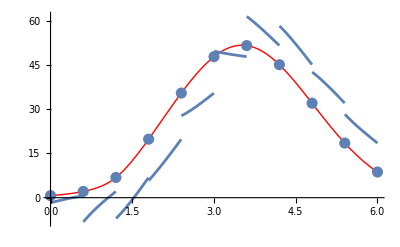

```mathematica
graphS=Plot[S[x],{x,a,b}];
Show[graph,graphD2,graphS, PlotRange->Full]
```

Интерполируем функцию сплайном с помощью функции Interpolation:

```mathematica
Sf[x_]=Interpolation[data,x,Method->"Spline"]
```

InterpolatingFunction[…][x]

Проиллюстрируем полученный сплайн:

```mathematica
graphSf=Plot[Sf[x],{x,a,b}];
```

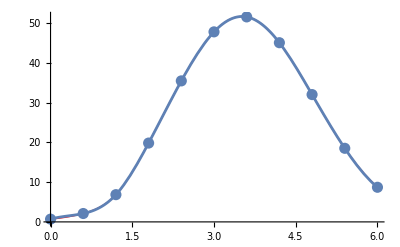

```mathematica
Show[graph,graphD2,graphSf]
```

в) Получим интерполяционный кубический сплайн с помощью функции SplineFit:

```mathematica
Needs["Splines`"]
```

```mathematica
Spl=SplineFit[data,Cubic];
```

Изобразим полученный сплайн.

```mathematica
t=(x-a)/h;
```

```mathematica
graphSpl=ParametricPlot[Spl[i],{i,0,n}];
```

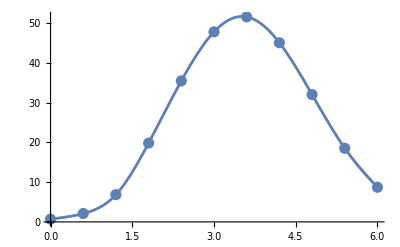

```mathematica
Show[graph,graphD2,graphSpl]
```

д) Вычислим значения функции f(x) и всех построенных интерполяционных многочленов S_3(x), Sf(x)  и Spl в точке x=2,4316:

```mathematica
f[2.4316]
```

36.288

```mathematica
S[2.4316]
```

28.0798

```mathematica
Sf[2.4316]
```

36.2877

```mathematica
Spl[(2.4316-a)/h2]
```

{2.4316,36.2873}

Задание 5. Используя таблицу значений функции f(x) в равноотстоящих точках отрезка [0, 6], полученной в задании 1 при 
n = 10, выполнить следующие действия:
	а) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом первой степени Q_1(x), проиллюстрировать
графически (изобразить точки (x_i, f(x_i)) и графики функций f(x) и Q_1(x) на одном чертеже);
	б) аппроксимировать с помощью метода наименьших квадратов функцию f(x) многочленом второй степениQ_2(x), проиллюстрировать
графически;
	в) найти многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней(Q_3(x) и Q_4(x)) с помощью функции Fit пакета Mathematica, проиллюстрировать графически;
	г) вычислить значения функции f(x) и построенных многочленов Q_1(x), Q_2(x), Q_3(x) и Q_4(x) в точке x = 2,4316;
	д) сравнить результаты, полученные в пунктах а, б и в, изобразив на одном чертеже точки (x_i, f(x_i)) и графики функций Q_1(x), Q_2(x), Q_3(x) и Q_4(x).

а) Аппроксимируем с помощью метода наименьших квадратов функцию многочленом первой степени:

Коэффициенты каждой строки системы относительно a_i:

```mathematica
ACoeff1=Table[If[i+j!=0,∑_(k=0)^n2 (data[[k+1,1]])^(i+j),n2+1], {i, 0, 1}, {j, 0, 1}]
```

{{11,33.},{33.,138.6}}

Столбец свободных членов:

```mathematica
B1:=Table[If[i!=0,∑_(k=0)^n2 (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n2 data[[l+1,2]]], {i, 0, 1}]
```

Найдём значения a_i с помощью встроенной функции LinearSolve:

```mathematica
A1=LinearSolve[ACoeff1,B1]
```

{13.1716,3.75838}

Тогда многочлен примет вид:

```mathematica
Q1[x_]=∑_(i=0)^1 (A1[[i+1]]*x^i)
```

13.1716+3.75838 x

Проиллюстрируем полученный многочлен:

```mathematica
graphQ1=Plot[Q1[x],{x,a,b},PlotStyle->Green];
```

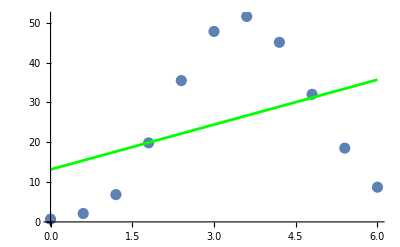

```mathematica
Show[graphD2,graphQ1]
```

б) Аппроксимируем с помощью метода наименьших квадратов функцию многочленом второй степени:

```mathematica
ACoeff2=Table[If[i+j!=0,∑_(k=0)^n2 (data[[k+1,1]])^(i+j),n2+1], {i, 0, 2}, {j, 0, 2}]
```

{{11,33.,138.6},{33.,138.6,653.4},{138.6,653.4,3283.16}}

Столбец свободных членов:

```mathematica
B2:=Table[If[i!=0,∑_(k=0)^n2 (data[[k+1,2]]*(data[[k+1,1]])^i), ∑_(l=0)^n2 data[[l+1,2]]], {i, 0, 2}]
```

Найдём значения a_i с помощью встроенной функции LinearSolve:

```mathematica
A2=LinearSolve[ACoeff2,B2]
```

{-11.763,31.4635,-4.61752}

Тогда многочлен примет вид:

```mathematica
Q2[x_]=∑_(i=0)^2 (A2[[i+1]]*x^i)
```

-11.763+31.4635 x-4.61752 x^2

Проиллюстрируем полученный многочлен:

```mathematica
graphQ2=Plot[Q2[x],{x,a,b},PlotStyle->Red];
```

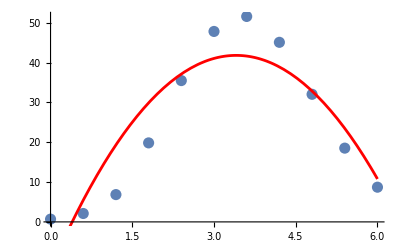

```mathematica
Show[graphD2,graphQ2]
```

в) Построим многочлены наилучшего среднеквадратичного приближения третьей и четвертой степеней с помощью встроенной функции Fit:

```mathematica
Q3[x_]=Fit[data,{1,x^1,x^2,x^3},x]
```

-3.23903+8.89084 x+5.24814 x^2-1.09618 x^3

```mathematica
Q4[x_]=Fit[data,{1,x^1,x^2,x^3,x^4},x]
```

2.41956-23.8556 x+32.5369 x^2-8.37318 x^3+0.606416 x^4

Изобразим полученные многочлены:

```mathematica
graphQ3=Plot[Q3[x],{x,a,b},PlotStyle->Yellow];
```

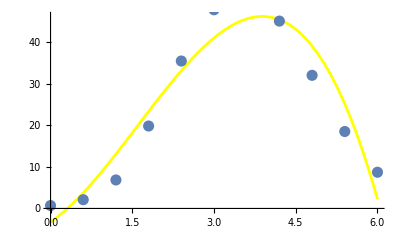

```mathematica
Show[graphQ3,graphD2]
```

```mathematica
graphQ4=Plot[Q4[x],{x,a,b}, PlotStyle->Blue];
```

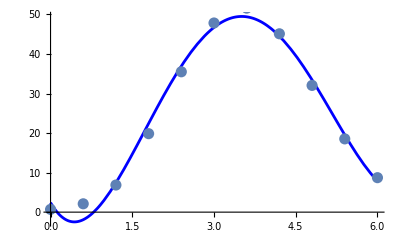

```mathematica
Show[graphQ4,graphD2]
```

г) Вычислим значения функции f(x) и всех построенных интерполяционных многочленов Q_1(x), Q_2(x),Q_3(x) и Q_4(x)  в точке x=2,4316:

```mathematica
f[2.4316]
```

36.288

```mathematica
Q1[2.4316]
```

22.3105

```mathematica
Q2[2.4316]
```

37.4417

```mathematica
Q3[2.4316]
```

33.6504

```mathematica
Q4[2.4316]
```

37.609

д) По вычисленным значениям и графикам полученных функций можно заметить, что при увеличении степени многочлена улучшается точность приближения.

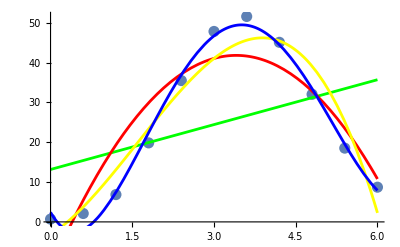

```mathematica
Show[graphD2,graphQ1,graphQ2,graphQ3,graphQ4]
```